```mathematica
(* MA39110 / Assignment 2.3 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
Thomas[a_,b_,c_,d_]:=Module[{c1=Range[Length[c]],d1=Range[Length[d]],x=Range[Length[b]]},
c1[[1]]=c[[1]]/b[[1]]; d1[[1]]=d[[1]]/b[[1]];
Do[
If[i≠Length[d],c1[[i]]=c[[i]]/(b[[i]]-a[[i-1]]*c1[[i-1]])];
d1[[i]]=(d[[i]]-a[[i-1]]*d1[[i-1]])/(b[[i]]-a[[i-1]]*c1[[i-1]]);
,{i,2,Length[d]}];
x[[Length[b]]]=d1[[Length[b]]];
Do[
x[[i]]=d1[[i]]-c1[[i]]*x[[i+1]];
,{i,Length[b]-1,1,-1}];
x];
Model[n0_]:=Module[{n=n0},
x0=0;xf=1;h=(xf-x0)/n;
A=Table[0,{x,0,n},{y,0,n}];
X =Table[x0+x*h,{x,0,n}];
B =Table[-4*(x0+x*h)*h^2,{x,0,n}];
For[i=1,i<n+2,i++,
{
A[[i,i]]=-(2+2*h^2);
If[i≠1,A[[i,i-1]]=1+X[[i]]*h];
If[i≠n+1,A[[i,i+1]]=1-X[[i]]*h];
}];
A[[1,1]]=A[[1,1]]+(1+X[[1]]*h)*(-2*h);
A[[1,2]]=A[[1,2]]+(1+X[[1]]*h);
A[[n+1,n+1]]=A[[n+1,n+1]]+(1-X[[n+1]]*h)*(4*h);A[[n+1,n]]=A[[n+1,n]]+(1-X[[n+1]]*h);B[[n+1]]=B[[n+1]]+(1-X[[n+1]]*h)*(2*h);
Thomas[Diagonal[A,-1],Diagonal[A],Diagonal[A,1],B]];
```

```mathematica
sol=N[Model[10]];
solt=DSolve[{y''[x]-2*x*y'[x]-2*y[x]==-4*x,y[0]-y'[0]==0,2*y[1]-y'[1]==1},y[x],x]
err1=DSolveValue[{y''[x]-2*x*y'[x]-2*y[x]==-4*x,y[0]-y'[0]==0,2*y[1]-y'[1]==1},y[X],x]-sol;
perr1 = ListPlot[Transpose[{X,err1}],PlotStyle->Red];
N[Max[err1]]
p1=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18],PlotStyle->Black]},{ListPlot[Transpose[{X,sol}],PlotStyle->Red]}];
```

{{y[x]→ⅇ^(x^2)+x}}

0.345276

```mathematica
sol=Model[50];
err2=DSolveValue[{y''[x]-2*x*y'[x]-2*y[x]==-4*x,y[0]-y'[0]==0,2*y[1]-y'[1]==1},y[X],x]-sol;
perr2 = ListPlot[Transpose[{X,err2}],PlotStyle->Green];
N[Max[err2]]
p2=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18],PlotStyle->Black]},{ListPlot[Transpose[{X,sol}],PlotStyle->Green]}];
```

0.0157582

```mathematica
sol=Model[100];
err3=DSolveValue[{y''[x]-2*x*y'[x]-2*y[x]==-4*x,y[0]-y'[0]==0,2*y[1]-y'[1]==1},y[X],x]-sol;
perr3=ListPlot[Transpose[{X,err3}],PlotStyle->Blue];
N[Max[err3]]
p3=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18],PlotStyle->Black]},{ListPlot[Transpose[{X,sol}],PlotStyle->Blue]}];
```

0.00395698

```mathematica
p4=Show[{perr1},{perr2},{perr3},{Plot[y[x]=10^-2,{x,0,1}]},PlotLabel->Style["Truncation Error",FontSize->18],PlotRange->{{0,1},{0,0.35}},AspectRatio->3.75];
N[sol[[-1]]]
```

3.71432

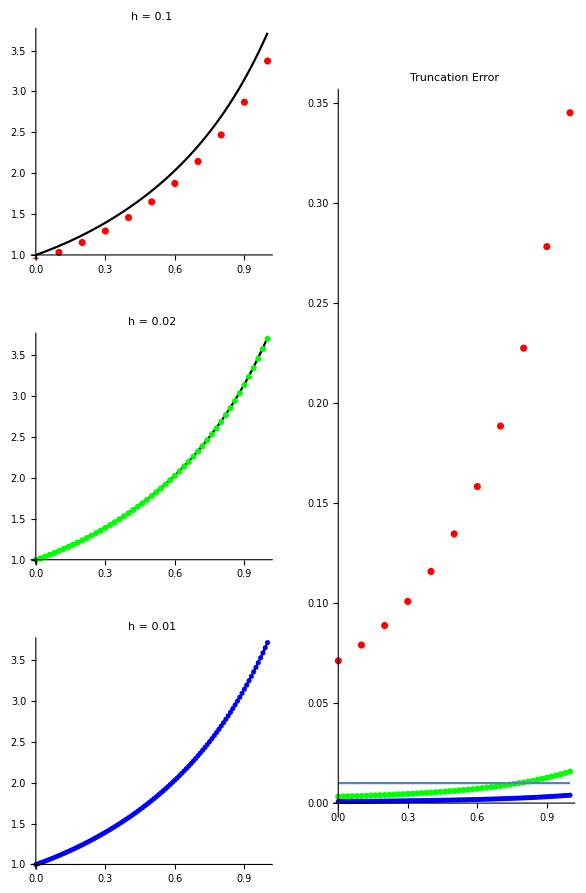

```mathematica
GraphicsGrid[{{p1,p4},{p2,SpanFromAbove},{p3,SpanFromAbove}}]
```